## Import

```mathematica
<<WebSocketJLink`
```

## Basic usage

```mathematica
connection = WebSocketConnect["wss://stream.binance.com:9443/ws/btcusdt@miniTicker"]
```

WebSocketConnectionObject[…]

```mathematica
WebSocketClose[connection]
```

WebSocketConnectionObject[…]

```mathematica
ImportString[Last[Normal[connection["Data"]]], "JSON"]
```

{e→24hrMiniTicker,E→1648160046435,s→BTCUSDT,c→44005.50000000,o→42368.99000000,h→44220.89000000,l→42365.07000000,v→57808.30162000,q→2502968576.04789690}

## Custom deserializer and event handler

```mathematica
ethusdtKlines = {}
```

{}

```mathematica
connection2 = WebSocketConnect["wss://stream.binance.com:9443/ws/ethusdt@miniTicker", 
"Deserializer"->Function[ImportString[#, "RawJSON"]], 
"EventHandler"->Function[AppendTo[ethusdtKlines, 
{FromUnixTime[#E / 1000], ToExpression[#c]}
]; 
]
]
```

WebSocketConnectionObject[…]

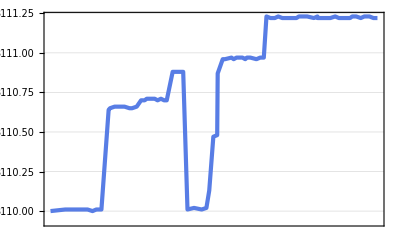

```mathematica
DateListPlot[ethusdtKlines, PlotTheme->"Business",Frame->True]
```

```mathematica
WebSocketClose[connection2]
```

WebSocketConnectionObject[…]